## Special classes of convex models

## Linear programs

### linear constraints

```mathematica
linearInEqConstraints =ImplicitRegion[x +y ≤  1 && 3x -y ≤  2 && -x +4y ≤    1&& x ≥    0&& y ≥ 0,{x,y}];
linearEqConstraints =ImplicitRegion[x +y  ==1/2,{x,y}]
RegionPlot[{linearEqConstraints,linearInEqConstraints},ImageSize->Small]
```

ImplicitRegion[x+y==1/2,{x,y}]

-Graphics-

### linear objective function

```mathematica
linearObjective[x_,y_]:= 3x + 4y
```

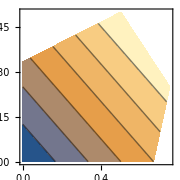
-Graphics--Graphics3D-

```mathematica
Row[{ContourPlot[linearObjective[x,y],{x,y}∈ linearConstraints,ImageSize->Small],Plot3D[linearObjective[x,y],{x,y}∈ linearConstraints,ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->Small]}]
```

## Linear Constrained Quadratic programs

```mathematica
Q1 = ({{2, 2}, {-4, 3}}); C1 = {-2,3};B1 = -1;
Q2 = ({{1, 2}, {-1, 3}}); C2 = {1,-2};B2 = 1;
X = {x,y};
constraint1 =X.Q1.X + C1 . X + B1<=   1;
constraint2 =X.Q2.X + C2 . X + B2<=   2;
```

```mathematica
PositiveSemidefiniteMatrixQ[Q1]
```

True

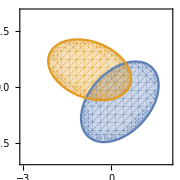

```mathematica
RegionPlot[{constraint1,constraint2},{x,-3,2},{y,-2,2},ImageSize->Small]
```

```mathematica
QuadraticOptimization
```

## Geometric programs

This is a text cell.

## Second-order cone programs

This is a text cell.

## Semidefinite programs

This is a text cell.